```mathematica
data={{0.01901837010356782,-0.004240972516457934},{0.09697504027482194,-0.00601616959757974},{0.13581832892216866,-0.007460111237406394},{0.16579830670461462,-0.008555310941671345},{0.19113225405730064,-0.009284252421532167},{0.21348067494724568,-0.009627781895305356},{0.23370164443332148,-0.00956407611586491},{0.2523071910305881,-0.009067902306972292},{0.26963193186388873,-0.008109906826303344},{0.2859087944005217,-0.006655747141783391},{0.3013076480119063,-0.004664944251975293},{0.3159568938722083,-0.002089369774674493}};
moms=data[[All,1]]
Xi=data[[All,2]]
dim=Length[Xi]
```

{0.0190184,0.096975,0.135818,0.165798,0.191132,0.213481,0.233702,0.252307,0.269632,0.285909,0.301308,0.315957}

{-0.00424097,-0.00601617,-0.00746011,-0.00855531,-0.00928425,-0.00962778,-0.00956408,-0.0090679,-0.00810991,-0.00665575,-0.00466494,-0.00208937}

12

```mathematica
Nn=IntegerPart[(dim)/2]-1;
Mm=IntegerPart[(dim)/2]+Mod[(dim),2]-1;

coffs={Array[cn,Nn+1],Array[cm,Mm+1]};
inicoffs=Transpose[{Flatten[coffs],RandomReal[{0.01,1.2},Length[Flatten[coffs]]]}];

modelP=Sum[coffs[[1]][[i+1]] k^(2 i),{i,0,Nn}]
modelQ=Sum[coffs[[2]][[i+1]] k^(2 i),{i,0,Mm}]
modelX=modelP/modelQ
```

cn[1]+k^2 cn[2]+k^4 cn[3]+k^6 cn[4]+k^8 cn[5]+k^10 cn[6]

cm[1]+k^2 cm[2]+k^4 cm[3]+k^6 cm[4]+k^8 cm[5]+k^10 cm[6]

(cn[1]+k^2 cn[2]+k^4 cn[3]+k^6 cn[4]+k^8 cn[5]+k^10 cn[6])/(cm[1]+k^2 cm[2]+k^4 cm[3]+k^6 cm[4]+k^8 cm[5]+k^10 cm[6])

```mathematica
eqs=(modelP==Xi[[#]] modelQ)/.k->(moms[[#]]^2)&/@Range[Length[moms]];
c=CoefficientArrays[eqs,Variables@eqs];
MatrixForm@c[[2]];
Det@c[[2]];
```

```mathematica
solu=FindFit[data,modelX,inicoffs,k]
```

{cn[1]→-0.384662,cn[2]→-21.9479,cn[3]→29.6673,cn[4]→-770.231,cn[5]→12111.4,cn[6]→132647.,cm[1]→92.3927,cm[2]→493.357,cm[3]→9562.9,cm[4]→25439.4,cm[5]→-33098.4,cm[6]→-616674.}

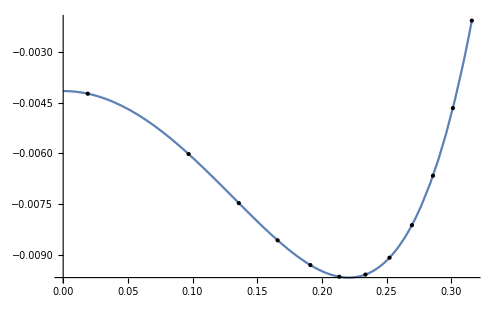

```mathematica
P2[mom_]:=modelX/.solu/.k->mom
Plot[P2[t],{t,0,moms[[-1]]},Epilog->Map[Point,data],PlotRange->Automatic,ImageSize->500]
```

```mathematica
Ll=1;
FindRoot[(modelP-I k^(2 Ll+1) modelQ)/.solu,{k,1-0.98 I}]
```

{k→0.21374-0.231703 ⅈ}